# Analytic forms

## Convert params to moments

```mathematica
varh={{varh11}};
varhInv=Inverse[varh];
wt={{wt11,wt12}};
b={b1,b2};
muh={muh1};
```

```mathematica
nv=2;
nh=1;
```

```mathematica
varvh=varh.wt;
varv=Transpose[wt].varh.wt+sig2*IdentityMatrix[nv];
muv=b+Transpose[wt].muh;

mu=Join[muv,muh];
var=ArrayFlatten[{{varv,Transpose[varvh]},{varvh,varh}}];

nvar=Simplify[var+KroneckerProduct[mu,mu]];

n=nv+nh;

nMoments3=Association[];
Do[
Do[
Do[
nMoments3[{in,jn,kn}]=Simplify[-2*mu[[in]]*mu[[jn]]*mu[[kn]]+mu[[in]]*nvar[[jn,kn]]+mu[[jn]]*nvar[[in,kn]]+mu[[kn]]*nvar[[in,jn]]];
,{kn,jn,n}];
,{jn,in,n}];
,{in,n}];
```

## NMomentsTE to MomentsTE

```mathematica
muTE={muTE1,muTE2,muTE3};
nvarTE={{nvarTE11,nvarTE12,nvarTE13},{nvarTE12,nvarTE22,nvarTE23},{nvarTE13,nvarTE23,nvarTE33}};
varTE=Simplify[nvarTE-(KroneckerProduct[muTE,mu]+KroneckerProduct[mu,muTE])];
```

## MomentsTE to ParamMomentsTE

```mathematica
muvTE=muTE[[;;nv]];
muhTE=muTE[[nv+1;;]];

varvhTE=varTE[[nv+1;;,;;nv]];
varvbarTE=Total[Diagonal[varTE[[;;nv,;;nv]]]];
varhTE=varTE[[nv+1;;,nv+1;;]];
```

## ParamMomentsTE to ParamsTE

```mathematica
bTE=Simplify[muvTE-Transpose[varvhTE].varhInv.muh+Transpose[varvh].varhInv.varhTE.varhInv.muh-Transpose[varvh].varhInv.muhTE];
wtTE=Simplify[-varhInv.varhTE.varhInv.varvh+varhInv.varvhTE];

m=Transpose[varvhTE].varhInv.varvh-Transpose[varvh].varhInv.varhTE.varhInv.varvh+Transpose[varvh].varhInv.varvhTE;
sig2TE=Simplify[(1/nv)*varvbarTE-(1/nv)*Total[Diagonal[m]]];
```

## Death

```mathematica
makeRepsDeath[iSp_]:=Module[
{muTEreps,nvarTEreps,x}
,
muTEreps=Table[
x=ToExpression["muTE"<>ToString[jSp]];
If[jSp==iSp,
x->-mu[[iSp]],
x->0
],{jSp,n}];

nvarTEreps=Flatten[Table[
x=ToExpression["nvarTE"<>ToString[Min[jSp,kSp]]<>ToString[Max[jSp,kSp]]];
If[jSp==iSp&&kSp==iSp,
x->-2*nvar[[iSp,iSp]]+mu[[iSp]],
If[jSp==iSp||kSp==iSp,
x->-nvar[[jSp,kSp]],
x->0
]
]
,{jSp,n},{kSp,jSp,n}]];

Return[Join[muTEreps,nvarTEreps]];
]
```

```mathematica
eqs=Flatten[Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsDeath[3]]]
```

{(muh1^2 wt11)/varh11,(muh1^2 wt12)/varh11,wt11-(muh1 wt11)/varh11,wt12-(muh1 wt12)/varh11,1/2 muh1 (wt11^2+wt12^2),-muh1,muh1-2 varh11}

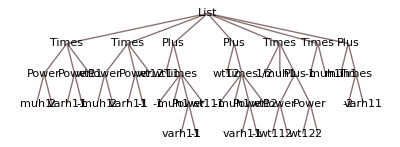

52

```mathematica
tf=TreeForm[eqs]
Length[Level[tf,Depth[tf]]]-1
```

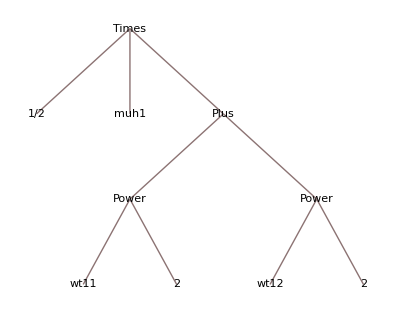

10

```mathematica
tf=TreeForm[eqs[[5]]]
Length[Level[tf,Depth[tf]]]
```

## Eat

```mathematica
getNMoment3[idxs_]:=nMoments3[Sort[idxs]]
```

```mathematica
makeRepsEat[iHunter_,iPrey_]:=Module[
{muTEreps,nvarTEreps,x,y}
,
muTEreps=Table[
x=ToExpression["muTE"<>ToString[jSp]];
If[jSp==iPrey,
x->-nvar[[iHunter,iPrey]],
If[jSp==iHunter,
x->nvar[[iHunter,iPrey]],
x->0
]],{jSp,n}];

nvarTEreps={};
Do[
x=ToExpression["nvarTE"<>ToString[Min[jSp,kSp]]<>ToString[Max[jSp,kSp]]];

If[jSp==iPrey&&kSp==iPrey,
y=-2*getNMoment3[{iPrey,iPrey,iHunter}]+nvar[[iHunter,iPrey]];
AppendTo[nvarTEreps,x->y];
];

If[jSp==iHunter&&kSp==iHunter,
y=2*getNMoment3[{iHunter,iHunter,iPrey}]+nvar[[iHunter,iPrey]];
AppendTo[nvarTEreps,x->y];
];

If[(jSp==iHunter&&kSp==iPrey)||(jSp==iPrey&&kSp==iHunter),
y=-getNMoment3[{iHunter,iHunter,iPrey}]+getNMoment3[{iHunter,iPrey,iPrey}]-nvar[[iHunter,iPrey]];
AppendTo[nvarTEreps,x->y];
];

If[kSp==iPrey&&(jSp≠iHunter&&jSp≠iPrey),
y=-getNMoment3[{jSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

If[jSp==iPrey&&(kSp≠iHunter&&kSp≠iPrey),
y=-getNMoment3[{kSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

If[kSp==iHunter&&(jSp≠iHunter&&jSp≠iPrey),
y=getNMoment3[{jSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

If[jSp==iHunter&&(kSp≠iHunter&&kSp≠iPrey),
y=getNMoment3[{kSp,iPrey,iHunter}];
AppendTo[nvarTEreps,x->y]
];

,{jSp,n},{kSp,jSp,n}];

Return[Simplify[Join[muTEreps,nvarTEreps]]];
]
```

```mathematica
eqs=Flatten[Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsEat[3,1]]]
```

{1/varh11(b1 muh1^2 (1+wt11)+muh1^3 wt11 (1+wt11)+muh1 varh11 wt11 (1+wt11)-varh11^2 wt11 (1+wt11)+muh1^2 (-sig2+varh11 wt11 (1+wt11))),((b1 muh1^2+(muh1^3+muh1 varh11+muh1^2 varh11-varh11^2) wt11) wt12)/varh11,-1/varh11(-muh1 sig2+b1 (muh1+varh11) (1+wt11)+muh1^2 wt11 (1+wt11)+varh11 wt11 (1+wt11)+2 muh1 varh11 wt11 (1+wt11)),-((b1 (muh1+varh11)+(muh1^2+varh11+2 muh1 varh11) wt11) wt12)/varh11,1/2 (nvarTE22-2 muh1 sig2+muh1^2 wt11-2 muh1 sig2 wt11+varh11 wt11+2 muh1^2 wt11^2+2 varh11 wt11^2+muh1^2 wt11^3+varh11 wt11^3+muh1^2 wt11 wt12^2+varh11 wt11 wt12^2+b1 muh1 (1+2 wt11+wt11^2+wt12^2)),b1 muh1+(muh1^2+varh11) wt11,b1 (muh1+2 varh11)+(muh1^2+varh11+4 muh1 varh11) wt11}

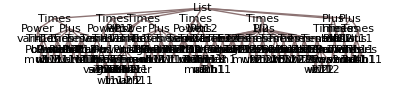

249

```mathematica
tf=TreeForm[eqs]
Length[Level[tf,Depth[tf]]]-1
```

## Birth

```mathematica
makeRepsBirth[iSp_]:=Module[
{muTEreps,nvarTEreps,x}
,
muTEreps=Table[
x=ToExpression["muTE"<>ToString[jSp]];
If[jSp==iSp,
x->mu[[iSp]],
x->0
],{jSp,n}];

nvarTEreps=Flatten[Table[
x=ToExpression["nvarTE"<>ToString[Min[jSp,kSp]]<>ToString[Max[jSp,kSp]]];
If[jSp==iSp&&kSp==iSp,
x->2*nvar[[iSp,iSp]]+mu[[iSp]],
If[jSp==iSp||kSp==iSp,
x->nvar[[jSp,kSp]],
x->0
]
]
,{jSp,n},{kSp,jSp,n}]];

Return[Join[muTEreps,nvarTEreps]];
]
```

# All reactions

```mathematica
noNodes={};
Do[
eqs=Flatten[Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsBirth[i]]];
tf=TreeForm[eqs];
AppendTo[noNodes,Length[Level[tf,Depth[tf]]]-1];
,{i,1,3}];

Do[
eqs=Flatten[Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsDeath[i]]];
tf=TreeForm[eqs];
AppendTo[noNodes,Length[Level[tf,Depth[tf]]]-1];
,{i,1,3}];

Do[
Do[
If[i≠j,
eqs=Flatten[Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsEat[i,j]]];
tf=TreeForm[eqs];
AppendTo[noNodes,Length[Level[tf,Depth[tf]]]-1];
];
,{j,1,3}];
,{i,1,3}];

noNodes
Total[noNodes]
Mean[noNodes]//N
```

{16,16,50,20,20,52,137,251,135,249,249,247}

1442

120.167

## By ixns

```mathematica
eqsIxns=<|
"b"->{},
"wt"->{},
"sig2"->{},
"muh"->{},
"varh"->{}
|>;
Do[
eq=Association[];
{eq["b"],eq["wt"],eq["sig2"],eq["muh"],eq["varh"]}=Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsBirth[i]];
Do[
AppendTo[eqsIxns[k],eq[k]];
,{k,Keys[eq]}];
,{i,1,3}];

Do[
eq=Association[];
{eq["b"],eq["wt"],eq["sig2"],eq["muh"],eq["varh"]}=Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsDeath[i]];
Do[
AppendTo[eqsIxns[k],eq[k]];
,{k,Keys[eq]}];
,{i,1,3}];

Do[
Do[
If[i≠j,
eq=Association[];
{eq["b"],eq["wt"],eq["sig2"],eq["muh"],eq["varh"]}=Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsEat[i,j]];
Do[
AppendTo[eqsIxns[k],eq[k]];
,{k,Keys[eq]}];
];
,{j,1,3}];
,{i,1,3}];

Do[
eqsIxns[k]=Flatten[eqsIxns[k]];
,{k,Keys[eqsIxns]}];

eqs=Flatten[Values[eqsIxns]];
```

```mathematica
makeTree[nodes_]:=Module[
{counter=0,tg},
traverse[h_[childs___]]:=With[{id=counter},{UndirectedEdge[id,++counter],traverse[#]}&/@{childs}];
traverse[_]:=Sequence[];
tg=TreeGraph[#,GraphLayout->"RadialEmbedding"]&@Flatten[traverse[nodes]];
Return[tg]
]
```

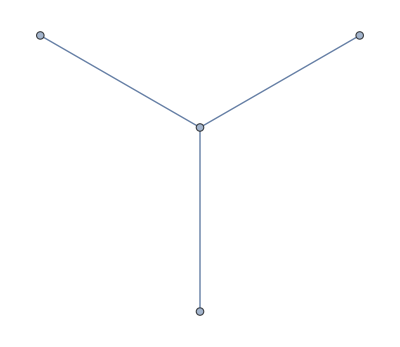

```mathematica
tf=TreeForm[eqs[[10]]];
makeTree[tf]
```

```mathematica
makeTreeNodes[nodes_,counterStart_]:=Module[
{counter=counterStart},
traverse[h_[childs___]]:=With[{id=counter},{UndirectedEdge[id,++counter],traverse[#]}&/@{childs}];
traverse[_]:=Sequence[];
Return[{Flatten[traverse[nodes]],counter}]
]
```

```mathematica
countersStart=Association[];
nodes=Association[];
countersStart[1]=0;
edgeColors={};

colors=<|
"b"->Blue,
"wt"->Red,
"sig2"->Darker[Cyan],
"muh"->Magenta,
"varh"->Darker[Green]
|>;

eqCtr=1;
Do[
Do[
tf=TreeForm[eqsIxns[ixn][[rxnIdx]]];
{nodes[eqCtr],countersStart[eqCtr+1]}=makeTreeNodes[tf,countersStart[eqCtr]];
nodes[eqCtr]=nodes[eqCtr]/.{countersStart[eqCtr]->0};

Do[
AppendTo[edgeColors,node->colors[ixn]];
,{node,nodes[eqCtr]}];

eqCtr+=1;
,{rxnIdx,1,Length[eqsIxns[ixn]]}];
,{ixn,Keys[eqsIxns]}];
```

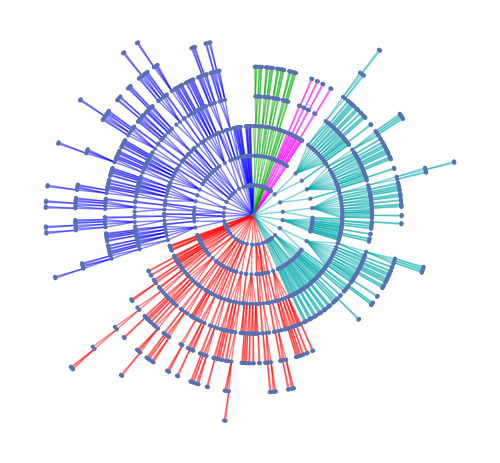
-Graphics- |

```mathematica
pIxn=TreeGraph[#,GraphLayout->"RadialEmbedding",EdgeStyle->edgeColors,ImageSize->500]&@Flatten[Values[nodes]];
legIxn=LineLegend[Values[colors],{"F_b^(approx.)","F_W^(approx.)","(F_(σ^2))^(approx.)","F_μ_h^(approx.)","F_Σ_h^(approx.)"}];
Grid[{{pIxn,legIxn}}]
```

## By rxns

```mathematica
eqsRxns=<|
"birth"->{},
"death"->{},
"eat"->{}
|>;
Do[
eq=Flatten[Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsBirth[i]]];
eqsRxns["birth"]=Join[eqsRxns["birth"],eq];
,{i,1,3}];

Do[
eq=Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsDeath[i]];
eqsRxns["death"]=Join[eqsRxns["death"],eq];
,{i,1,3}];

Do[
Do[
If[i≠j,
eq=Simplify[{bTE,wtTE,sig2TE,muhTE,varhTE}/.makeRepsEat[i,j]];
eqsRxns["eat"]=Join[eqsRxns["eat"],eq];
];
,{j,1,3}];
,{i,1,3}];

Do[
eqsRxns[k]=RandomSample[Flatten[eqsRxns[k]]];
,{k,Keys[eqsRxns]}];
```

```mathematica
countersStart=Association[];
nodes=Association[];
countersStart[1]=0;
edgeColors={};

colors=<|
"birth"->Blue,
"death"->Red,
"eat"->Darker[Cyan]
|>;

eqCtr=1;
Do[
Do[
tf=TreeForm[eqsRxns[rxn][[rxnIdx]]];
{nodes[eqCtr],countersStart[eqCtr+1]}=makeTreeNodes[tf,countersStart[eqCtr]];
nodes[eqCtr]=nodes[eqCtr]/.{countersStart[eqCtr]->0};

Do[
AppendTo[edgeColors,node->colors[rxn]];
,{node,nodes[eqCtr]}];

eqCtr+=1;
,{rxnIdx,1,Length[eqsRxns[rxn]]}];
,{rxn,Keys[eqsRxns]}];
```

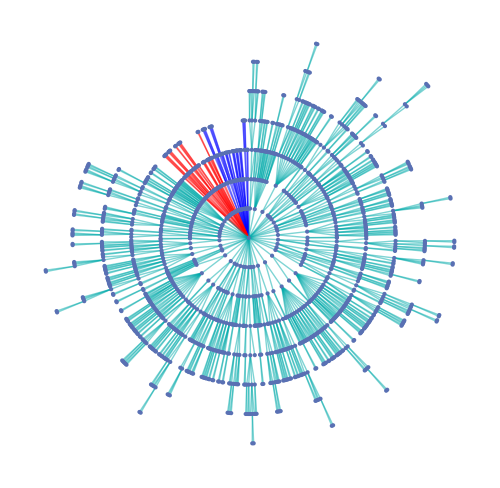
-Graphics- |

```mathematica
pRxn=TreeGraph[#,GraphLayout->"RadialEmbedding",EdgeStyle->edgeColors,ImageSize->500]&@Flatten[Values[nodes]];
legRxn=LineLegend[Values[colors],{"F_Birth^(approx.)","F_Death^(approx.)","(F_(Predator - Prey))^(approx.)"}];
Grid[{{pRxn,legRxn}}]
```

```mathematica
p=Grid[{{pIxn,legIxn,pRxn,legRxn}}]
```

-Graphics- |  | -Graphics- |

```mathematica
SetDirectory[NotebookDirectory[]];
Export["graphs.pdf",p]
Export["graphs.png",p,ImageResolution->80]
```

graphs.pdf

graphs.png